# Intro to persistent homology via Perseus

NOTE: feel free to evaluate the initialization cells, but do not evaluate the notebook before setting up the filepaths to the Perseus executable and data directory in the section “Making persistence diagrams with Perseus”.

What does Perseus do? It computes the persistent homology. Before we get to the “persistent” part, what is homology?

Homology is a property of a (sufficiently nice) shape. (Caveat: it’s actually more general, but we only care about the shape-related versions.)

Give me a shape (of any dimension) and I can tell you its homology groups.

There's a group associated with each dimension up to the dimension of the shape: H_0, H_1, H_2, etc.

Note: they exist but are trivial for all higher dimensions.

The group H_n associated with each dimension n tells us something about the n-dimensional quality of the shape in question. Specifically, it tells us how many n-dimensional holes the shape has.

### n-dimensional holes

Here’s an intuition for what an “n-dimensional hole” is: it’s when there’s a (floppy) sphere of dimension n in the shape which you can’t continuously contract to a point.

Note: Here a “sphere” means just the surface of a ball, so a 1-dimensional sphere is a closed curve.

```mathematica
Gaussian[σ_,μ_][x__]:=(1/(σ Sqrt[2Pi]))Exp[-Norm[{x}-μ]^2/(2σ^2)]
```

```mathematica
f[x_,y_]:=Gaussian[0.3,{-0.5,0}][x,y]+Gaussian[0.3,{0.5,0}][x,y]
```

```mathematica
fmax=Ceiling[f[0.5,0],0.1];
```

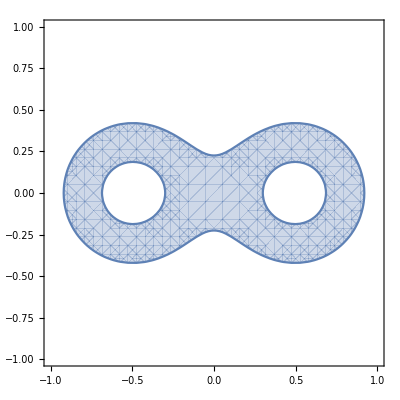

```mathematica
shape=RegionPlot[0.5<f[x,y]<1.1,{x,-1,1},{y,-1,1}]
```

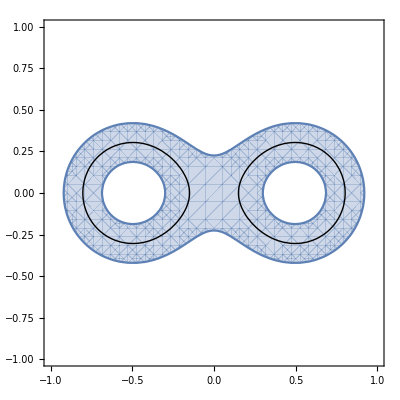

```mathematica
Show[shape,ContourPlot[{f[x,y]==0.8},{x,-1,1},{y,-1,1},ContourStyle->Directive[Black,Thick]]]
```

Above is a 2-dimensional shape in blue. It has two 1-dimensional holes, with examples of circles we cannot contract to a point while staying within the shape in black.

Because we cannot deform these circles into each other, these are indeed different holes. Conversely, if we could deform them into each other, then the two circles would represent the same hole.

Why doesn’t it have three? After all, the red curve below is also a circle we can’t deform into a point:

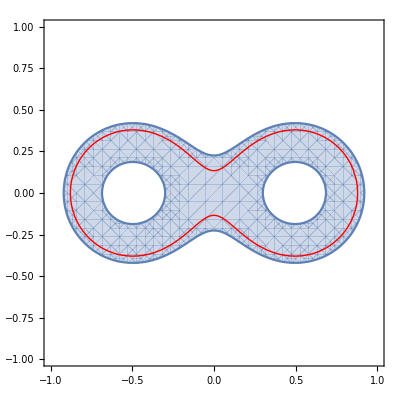

```mathematica
Show[shape,ContourPlot[{f[x,y]==0.6},{x,-1,1},{y,-1,1},ContourStyle->Directive[Red,Thick]]]
```

This is where homology differs from homotopy. In homology, we consider the hole represented by this dashed curve to be the sum of the two holes represented by the two black curves.

It’s kind of like how if we were integrating a curl-free vector field along these curves, we’d get the same answer  by adding the integrals over the two black curves as we would by integrating over the red curve (as long as you choose the right orientations). You can imagine deforming the two black curves into the red curve until they share a portion of their length, along which they’re oppositely-oriented—the integral each way over that part cancels out, leaving you with the red curve.

In the below, this overlap of oppositely-oriented lengths is shown as a dashed line. (Probably not really necessary since you know physics, but I wanted to make a slider...)

```mathematica
With[{overlap=Construct[Function,If[Re[#1]==0,Nothing,Line[{{0,Re[#1]},{0,Re[#2]}}]]&@@(y/.Quiet@Solve[f[0,y]==0.6*Slot[1]+0.8(1-Slot[1]),{y}])]},Manipulate[Show[shape,ContourPlot[{f[x,y]==0.6*v+0.8(1-v)},{x,-1,1},{y,-1,1},ContourStyle->{Directive[Blend[{Black,Red},v],Thick]}],Graphics[{Dashed,Thick,Blend[{Black,Red},v],overlap[v]}]],{{v,0.9},0,1}]]
```

That connection to physics is tantalizing, but ultimately irrelevant to us. We’re here to know about shapes and holes.

So, ordinary 1-dimensional holes (as above) are the things loops get stuck on.

What's a 0-dimensional hole? As it turns out: any connected component is a single 0-dimensional “hole”!

Aside: Not really a “hole”, sure, but the math makes this make sense. Behind the scenes, the defining quality of loops/n-dimensional spheres is that they have no boundary (unlike e.g. a 1D line segment, which has two 0D boundary points). The boundary of a point has to be a (-1)-dimensional thing, but there are none of those—so a point always has no boundary, and is in that way like a loop.

Two points represent the same 0D hole if you can deform them into each other, i.e. they’re in the same connected component.

What’s a 2D hole? It’s something a 2-dimensional sphere would get stuck on if you tried to contract it: i.e., a “bubble” of emptiness in a solid mass, a “void” enclosed by a shell, or, molecularly, a “cage”.

### Constructing & interpreting homology groups

Ok, great. So, how do the homology groups H_0, H_1, H_2, ... for each dimension n actually, practically encode the n-dimensional holes?

Luckily we don’t need group theory, because all of these “groups” are actually just ordinary* vector spaces! (Calling them “groups” is a holdover from the general case.)

*subject to terms and conditions. Could be a vector space over the field with two elements: then you don’t care about orientation. Could be a more general module over e.g. the integers. We don’t really care for now; you can think of them as ordinary real vector spaces.

And the encoding is very simple: the dimension of the vector space is the number of holes.

Well, why use vector spaces instead of just...counting the holes? Surely a number of holes suffices?

Vector spaces have the advantage of actually representing the relationship between the holes that we saw earlier. E.g. the holes represented by black loops above would correspond to basis vectors e_1, e_2, and the hole represented by the red loop is actually represented by e_1 + e_2.

You’ll notice we can change basis. We could think of the shape above as having two holes given by e_1 and e_1 + e_2. There’s nothing fundamental separating the black loops from the red loops. We just need to make a choice.

This choice of basis will be a meaningful detail later when understanding Perseus output, as Perseus (and persistent homology more generally) comes with a method of choosing a basis in the relevant cases.

So the point is: the vector space really does represent the space of holes as opposed to just their number.

This is also relevant for...

### Persistent homology

So given a shape, Perseus could just compute the homology.

But often that's too boring. We're not just given shapes in the real world. We're given pixel data, voxel data, etc.

So how do we make use of hole-counting in these dataful contexts?

We’ll start with 2D; everything generalizes immediately to 3D.

One way you might think to extract a shape from some grayscale pixel data is by applying a threshold. Just look at the shape made by the pixels with a grayscale value below 0.5.

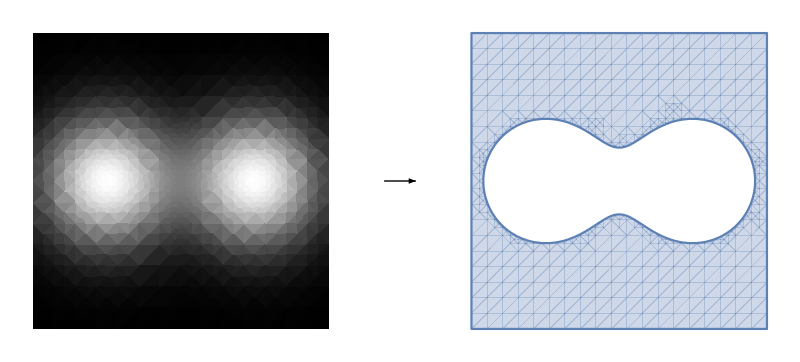

```mathematica
GraphicsRow[{
DensityPlot[f[x,y],{x,-1,1},{y,-1,1},ColorFunction->GrayLevel,Frame->False],
Graphics[{Arrowheads[0.5],Arrow[{{-0.1,0},{0.1,0}}]}],
RegionPlot[f[x,y]<0.5,{x,-1,1},{y,-1,1},Frame->False]}]
```

Ah-ha! We have a shape, and so can do homology to it.

It has one connected component and one 1D hole; that means its homology groups are:

H_0=[1D vector space];H_1=[1D vector space];H_2=0;H_3=0;...

Let’s also visualize this grayscale data as a graph.

```mathematica
Plot3D[f[x,y],{x,-1,1},{y,-1,1},Mesh->None,PlotRange->{0,fmax}]
```

-Graphics3D-

Now, the important part is that the threshold was arbitrary. So we want to scan through all thresholds, and see how the homology changes.

That is, our question to ask of the data is:

What homological features (holes) persist for what ranges of threshold values?

This is the sense in which Perseus computes the persistent homology. Its output tells you, roughly, at what threshold value holes of a given dimension appear, and at what threshold value they disappear.

Here’s an animation of scanning through the threshold values for this image.

```mathematica
display2D[f_,fmax_:1,range_:{{-1,1},{-1,1}}][v_]:=GraphicsRow[{
Plot3D[f[x,y],{x,Splice[range[[1]]]},{y,Splice[range[[2]]]},
PlotRange->{0,fmax},PlotTheme->"ZMesh",Mesh->{{v}},MeshShading->{Automatic,None},MeshStyle->Directive[Thick]],
RegionPlot[f[x,y]<=v,{x,Splice[range[[1]]]},{y,Splice[range[[2]]]}]}]
```

```mathematica
(*Should maybe just compute one mesh that's conveniently-sliced instead and share it between frames somehow, but space is cheap.*)displayExample=Array[display2D[f,fmax],48,{0,fmax}];
ListAnimate[displayExample,24]
```

The output of perseus tells you at what threshold a hole is born, and when it dies.

We can literally plot this: it’s a scatterplot of birth “times” (threshold values) vs. death times, each point representing a feature. This is called a persistence diagram, and is the main way of representing Perseus’ output. Ee’ll see them later.

Let’s see how the homology changes at different values.

First, there is nothing. All homology groups are the 0 vector space.

At a very low threshold value, we see just the four corners.

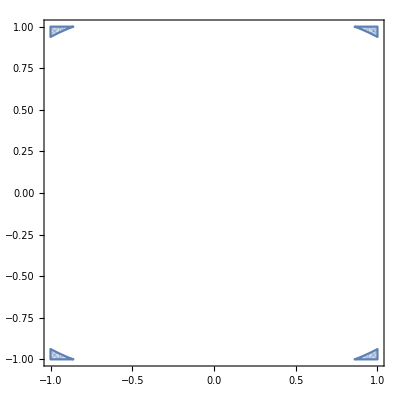

```mathematica
display2D[f,fmax][0.0025]
```

H_0=[4D];H_1=0

(I won’t spell out “vector space” anymore.)

By the way, we know that this surface can’t “close up” and form a 2D hole. (If it weren’t an image, but instead an abstract mathematical shape, it totally could.) So I won’t bother including H_2, which is always 0.

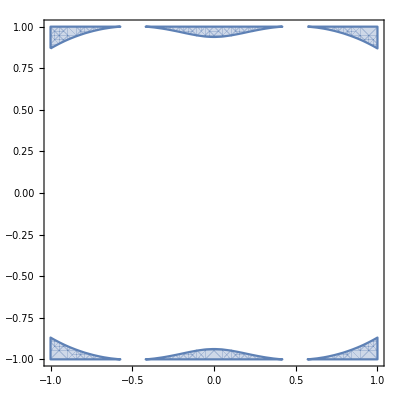

```mathematica
display2D[f,fmax][0.005]
```

Then those middle bits are born.

H_0=[6D];H_1=0

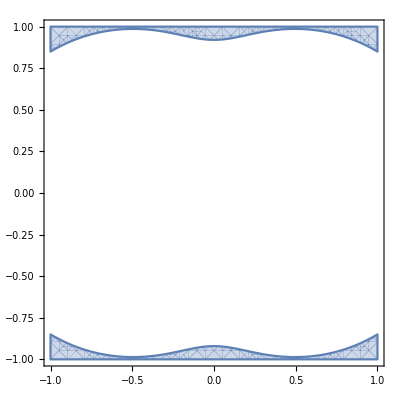

```mathematica
display2D[f,fmax][0.006]
```

Then they connect to each other!

H_0=[2D];H_1=0

As soon as they do, we’ve identified that four of these connected components—some basis elements in H_0—have died. But which?

The answer chosen by convention is “the ones that were most recently born”. In this case, that’s the blobs around x=0, plus either one of each set of corners. In our toy example the blobs at the corners were born at the same time, so we just choose arbitrarily (but this is an edge case).

Why do the most recently born die first? Because doing it this way lets us spot individual long-lasting features more easily (by letting the older ones live longer!), and persistence is what we care about.

For a while nothing changes, and then...

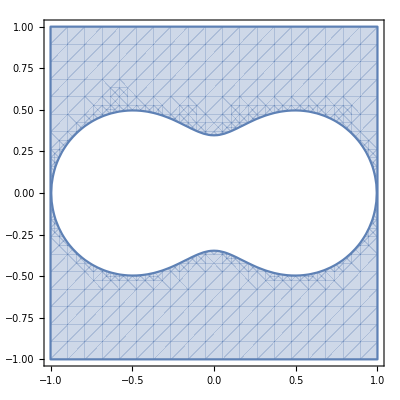

```mathematica
display2D[f,fmax][0.34]
```

Connection. Two things happen at this point:

H_0=[1D];H_1=[1D]

A connected component dies, and a 1D hole is born.

Nothing happens for a while, then...

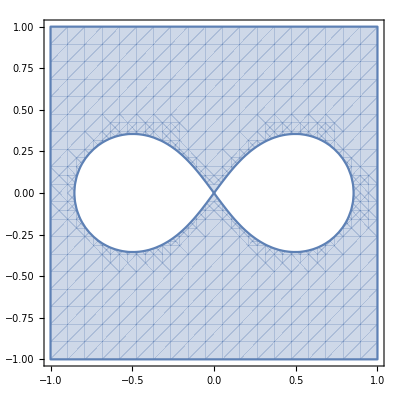

```mathematica
display2D[f,fmax][f[0,0]]
```

No connected component dies, but another hole is born.

H_0=[1D];H_1=[2D]

Note that this occurred at a critical point!

Note also that the existing 1D hole prior to this event isn’t considered to have died.

As above when considering the red and black loops, it’s fine to consider the two loops after this point to be “the one around both holes” and “a loop around just one of the holes”, as the loop around the other hole is a linear combination of these two.

Which smaller loop do we use? We’ll talk about that later. Doesn’t matter yet.

Nothing happens for a while...

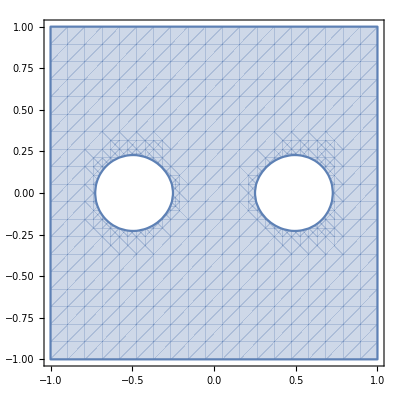

```mathematica
display2D[f,fmax][1]
```

H_0=[1D];H_1=[2D]

(Everything is the same here.)

Then the holes close up, both at the same time.

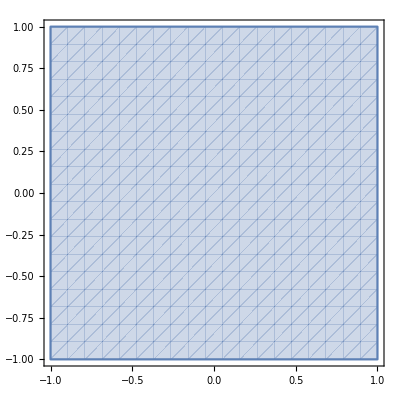

```mathematica
display2D[f,fmax][fmax]
```

H_0=[1D];H_1=0

As you can see, the connected component lives forever.

#### And in more depth...

Let’s recap what just happened in terms of theory:

At each threshold value t, we have a shape created by thresholding the image data. This shape has a sequence of homology groups (vector spaces) H_0(t), H_1(t), H_2(t)...

Increasing the threshold value gives us a new shape, which, since we’re increasing a threshold value, completely contains the old shape.

That inclusion of the shape image(t) in the shape image(t+1) induces linear maps between the homology groups of the shapes, i.e. linear maps H_n(t) → H_n(t+1) (for each n).

Why? Consider that a hole is represented by a loop, and a loop which is present in image(t) is also present in image(t+1), since thresholding only ever includes more pixels. It might suddenly be contractible (dies), or there might be some new loops that weren’t in image(t) (born). But either way there is a meaningful map of holes at time t to holes at time t+1 in a way that goes beyond counting.

Sometimes these linear maps indicate that:

some generator (i.e. basis vector) of H_n(t) is "born", i.e. the image of the linear map H_n(t) →  H_n(t + 1) is not the full H_n(t + 1)

or that some generator "dies", i.e. the null space of the map H_n(t) → H_n(t+1) is nontrivial, and some vectors have been sent to 0.

We look at the sequence of all those linear maps ... → H_n(t – 1) → H_n(t) → H_n(t+1) → H_n(t+2) → ..., and identify birth and death times for generators.

The magic of Perseus—and of persistent homology—is that you can do actually this. When a new dimension is added to H_n, i.e. some feature is born, you can choose the basis vector for that new dimension in such a way that you can see it persist through the sequence of maps until it dies (i.e. is sent to 0).

Aside: it’s known that you can’t do this nicely for more than one persistence parameter (i.e. two kinds of threshold value). :( But that doesn’t stop people from figuring out workarounds.

Perseus’s output discards the actual linear maps, and leaves us with just the pairs of (birth_time, death_time) of generators. Because that’s all you really need to see what features exist, and for how long.

### Making persistence diagrams with Perseus

#### Perseus hooks

Make sure these are set correctly if you want to use the following functions.

By default, it assumes the perseus executable is at ~/perseus/<executable>. The name will depend on your operating system.

Run $ConfirmPaths[] to check the relevant paths exist.

```mathematica
(*The path to the perseus executable.*)
$PerseusPath=FileNameJoin[{$HomeDirectory,"perseus","perseusMac"}];
(*Where files will be written to.*)
$DataDirectory=FileNameJoin[{$HomeDirectory,"perseus"}];
(*The filenames for the generated input data, output data, and metadata, nested under a folder in the $DataDirectory.*)
$InputName[_]:="input";
$OutputName[_]:="output";
$MDataName[_]:="mdata";
```

```mathematica
$ConfirmPaths[]:=Enclose[ConfirmBy[$DataDirectory,DirectoryQ];ConfirmBy[$PerseusPath,FileExistsQ];]
```

```mathematica
$ConfirmPaths[]
```

```mathematica
CreateInputFile[id_String]:=
If[FileExistsQ[#],#,CreateFile[#]]&[FileNameJoin[{$DataDirectory,id,$InputName[id]<>".txt"}]]
CreateInputFile[_]:=CreateFile[]
```

Documentation: RunPerseus[id][f, imageDims, dataRange, slice] runs Perseus (via $PerseusPath), and makes a folder named id in $DataDirectory.

It writes the calculated input data to id/$InputName[id].txt (simply id/input.txt by default) and the output data to files of the form id/$OutputName[id]_*.txt (where * is constructed by Perseus), typically simply id/output_*.txt.

imageDims are the dimensions of the resulting image (or voxel data, etc.). By default, it assumes a 2D image 50px by 50px.

dataRange is the range over which f will be sampled. E.g. the top-leftmost pixel is f[dataRange[[1,1]], dataRange[[2,1]]]. By default it is {{-1,1},{-1,1},...}, with the dimension inferred from imageDims.

slice discretizes the values of f[x,y,...] to multiples of slice. Perseus cannot accept floating point numbers as a technical limitation (some others can).

We entirely discard any negative values of f, removing them from the very shape of the image (pixels/voxels with negative values will never appear).

RunPerseus allows two “dry run” modes: RunPerseus[0][...], which only computes the input data and displays the image, and RunPerseus[1][...], which additionally prepares and prints the first 50 lines of the input file and writes it to a temporary directory (and deletes it).

```mathematica
PreprocessValues[val_,slice_]:=If[Negative[val],-1,Floor[val/slice]+1]
SetAttributes[PreprocessValues,Listable]
```

```mathematica
CompressWithDefinitions=ResourceFunction["CompressWithDefinitions"]
```

```mathematica
MDataFileName[id_String]:=FileNameJoin[{$DataDirectory,id,$MDataName[id]<>".txt"}]
```

```mathematica
toMetadata[id_,f_,imMax_,slice_,imageDims_,dataRange_]:=CompressWithDefinitions@<|"id"->id,"function"->f,"imMax"->imMax,"slice"->slice,"fmax"->imMax*slice,"imageDims"->imageDims,"dataRange"->dataRange|>
```

```mathematica
ReadMetadata[id_]:=Uncompress[ReadString[MDataFileName[id]]]
```

```mathematica
RunPerseus[id:(_String|0|1)][f_,slice_:0.1,
imageDims:{__Integer}:{50,50},
dataRange_:Automatic]:=
Enclose@Block[{range=Replace[Automatic:>ConstantArray[{-1,1},Length[imageDims]]]@dataRange},Block[
{im=PreprocessValues[Array[f,imageDims,range],slice],
imMax},
If[MatchQ[id,_String|1],
Block[{infile=CreateInputFile[id]},
(*(Over)write the input data file.*)
(*OpenWrite file to stream and Scan?*)
Put[Length[imageDims],Sequence@@imageDims,##,infile]&@@Flatten[im];
imMax=Max[im];
(*If not a dry run, run Perseus.*)
If[StringQ[id],
Block[{outfile=FileNameJoin[{$DataDirectory,id,$OutputName[id]}]},
PrintTemporary["Running Perseus..."];
ConfirmBy[
RunProcess[{$PerseusPath,"cubtop",infile,outfile}],
#["ExitCode"]==0&];
Print[outfile<>"_*"];
PrintTemporary["Cleaning up..."];
Block[{mdataFileName=MDataFileName[id]},
If[FileExistsQ[mdataFileName],DeleteFile[mdataFileName]];
WriteString[mdataFileName,toMetadata[id,f,imMax,slice,imageDims,range]]]
],
(* Print the first 20 lines of the constructed temporary input file on dry run mode 1, then delete it *)
FilePrint[infile,20];
DeleteFile[infile];
Echo@Uncompress[toMetadata["dry-run",f,imMax,slice,imageDims,range]]
]
]
];
Switch[Length[imageDims],
2,PrintTemporary["Drawing graph..."];ArrayPlot[Transpose@im,ColorRules->{-1->Pink},ColorFunction->GrayLevel],
3,PrintTemporary["Drawing graph..."];With[{max=If[ValueQ[imMax],imMax,Max[im]]},ListDensityPlot3D[im,RegionFunction->Function[{x,y,z,v},v>=0],ColorFunctionScaling->False,ColorFunction->(ColorData["BlueGreenYellow"][#/max]&)]],
_,im
]
]]
```

```mathematica
GetOutputFileName[id_String,n_Integer?NonNegative]:=FileNameJoin[{$DataDirectory,id,$OutputName[id]<>"_"<>ToString[n]<>".txt"}]
```

#### Running Perseus

We’ll run Perseus on our example.

/Users/thomas/perseus/example2D/output_*

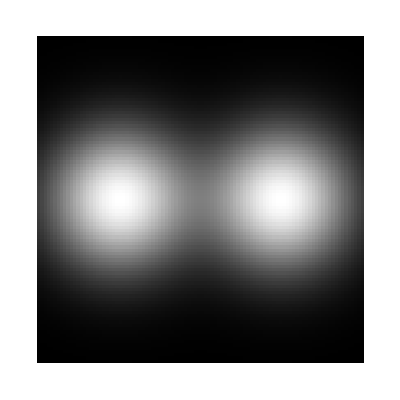

```mathematica
RunPerseus["example2D"][f,0.0025,{100,100}]
```

```mathematica
ReadPersistenceOutput[id_String]:=Block[{n=0,filename=GetOutputFileName[id,0]},Reap[
While[FileExistsQ[filename],
Sow@ReadList[filename,{Number,Number}];
n++;
filename=GetOutputFileName[id,n];]][[2,1]]]
```

Here are the contents of the text files produced by Perseus.

Note: Perseus also produces Betti numbers, but we don’t need those here. They’re derived from the homology information in a simple way anyway.

```mathematica
Block[{data=ReadPersistenceOutput["example2D"]},
Block[{filenames=FileNameJoin[{"example2D",$OutputName["example2D"]<>"_"<>ToString[#]<>".txt"}]&/@Range[0,Length[data]-1]},Grid[{filenames,Grid[#,Frame->True,Alignment->Left]&/@data},Frame->{All,False},Spacings->{1, 1}]]]
```

example2D/output_0.txt | example2D/output_1.txt | example2D/output_2.txt
2 | 3
2 | 3
1 | 3
1 | 3
1 | 133
1 | -1 | 266 | 534
133 | 534 |

Each dimension gets a file, and each line is a pair of integers (birth_time, death_time) for some generator (basis element) of the homology groups.

Now let’s visualize this output!

```mathematica
(*I don't feel like setting up real Options for PersistenceDiagram, but probably would if this were For Real.*)
PersistenceDiagram[pairs:{{_Integer,_Integer}...},slice_:1,fmax_:Automatic,extraOptions_List:{}]:=Block[{max=If[MatchQ[fmax,Automatic],Max[pairs,1]*slice,fmax]},
ListPlot[pairs*slice/.{x_,_?Negative}:>Style[{x,max},Red],
Sequence@@FilterRules[{
PlotRange->{{0,max},{0,max}},
PlotRangeClipping->False,
ImagePadding->Scaled[0.04],
AspectRatio->1,
PlotStyle->PointSize[Large],
Prolog->{Thin,Line[{{0,0},{max,max}}],
GrayLevel[0.96],Triangle[{{0,0},{max,max},{max,0}}]}},
Except[extraOptions]],
Sequence@@extraOptions]]
```

```mathematica
ReadPersistenceDiagrams[id_String,verbose2D_:False]:=Block[{output=Replace[ReadPersistenceOutput[id],{a___,{}..}:>{a}],mdata=ReadMetadata[id]},
With[{f=mdata["function"],range=mdata["dataRange"]},MapIndexed[PersistenceDiagram[#1,mdata["slice"],mdata["fmax"],
Append[PlotLabel->ToString[First[#2]-1]<>"D"]@
If[verbose2D&&(Length[mdata["dataRange"]]==2),{LabelingFunction->(pair|->Callout[Row[(v|->RegionPlot[f[x,y]<=v,{x,range[[1,1]],range[[1,2]]},{y,range[[2,1]],range[[2,2]]},ImageSize->30,Frame->False])/@pair],Automatic,LabelVisibility->All,Frame->True,FrameMargins->None]),
ImageSize->300},{}]]&,output]]]
```

We can plot these (birth, death) pairs in scatterplots, i.e. persistence diagrams.

0D comes first, then 1D (then 2D). We’ll use that convention everywhere going forward. (If I were doing this for real I’d include labels.)

Note that since death > birth, no dots are ever in the shaded region.

The red dot at the top of the 0D persistence indicates a connected component that never dies (i.e. death_time = infinity)

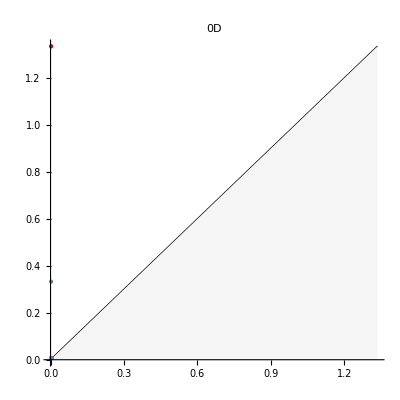
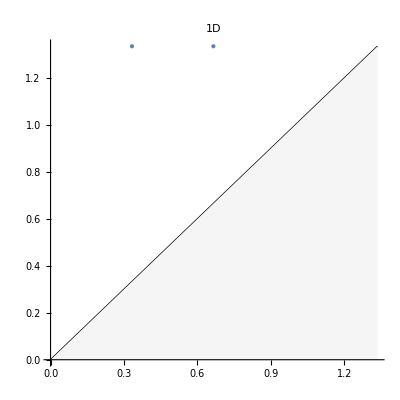

```mathematica
ReadPersistenceDiagrams["example2D"]
```

Reading these is something like:

All connected components get born pretty early.

Some die (i.e. merge with other connected components) early, and one does so a bit later.

One lives forever (expected).

On the 1D diagram, one hole is born at around 0.4, another at 0.6.

They both close up at the same time near the max.

Note that we’ve actually got a few dots superimposed in the bottom left.

Note also that they’re very close to the diagonal line. In general, the closer a generator is to the diagonal line, the more insignificant it is, since it died almost immediately after being born.

As such, in real situations, you often get rid of the noisy points near the diagonal.

Here, we’ll attach the thresholded image at the birth time and death time to each dot.

```mathematica
Column@ReadPersistenceDiagrams["example2D",True]
```

-Graphics-

Sometimes you see the persistence data presented instead as barcodes, but it’s less common. They’re quite illustrative, though.

```mathematica
BarcodeDiagram[pairs:{{_Integer,_Integer}...},slice_:1,fmax_:Automatic,extraOptions_List:{}]:=Block[{max=If[MatchQ[fmax,Automatic],Max[pairs,1]*slice,fmax]},
ListPlot[
MapIndexed[{pair,i}|->{#*slice,First[i]}&/@pair,pairs]/.{x_,{_?Negative,i_Integer}}:>Style[{x,{max,i}},Red],
Sequence@@FilterRules[{
PlotRange->{{0,max},Automatic},
Axes->{True,False},
Joined->True,
PlotStyle->Black},Except[extraOptions]],
Sequence@@extraOptions]]
```

```mathematica
ReadBarcodeDiagrams[id_String,verbose:True|False|{___Integer}:False,cleanupOutput_:(#&)]:=Block[{output=Replace[ReadPersistenceOutput[id],{a___,{}..}:>{a}],mdata=ReadMetadata[id]},MapIndexed[BarcodeDiagram[cleanupOutput[#1,First[#2]-1,mdata],mdata["slice"],mdata["fmax"],
Append[PlotLabel->ToString[First[#2]-1]<>"D"]@If[MatchQ[verbose,True]||(MatchQ[verbose,_List]&&MemberQ[verbose,First[#2]-1]),
Switch[Length[mdata["dataRange"]],
(*TODO: clean up*)
2,With[{f=mdata["function"],range=mdata["dataRange"]},{LabelingFunction->(pt|->Callout[RegionPlot[f[x,y]<=First[pt],{x,range[[1,1]],range[[1,2]]},{y,range[[2,1]],range[[2,2]]},ImageSize->30,Frame->False],Automatic,LabelVisibility->All,Frame->True,FrameMargins->None]),
ImageSize->300}],
3,With[{f=mdata["function"],range=mdata["dataRange"]},
{LabelingFunction->(pt|->Callout[RegionPlot3D[f[x,y,z]<=First[pt],{x,range[[1,1]],range[[1,2]]},{y,range[[2,1]],range[[2,2]]},{z,range[[3,1]],range[[3,2]]},PlotStyle->Opacity[0.2],Mesh->None,Axes->False],Automatic,LabelVisibility->All,Frame->True,FrameMargins->None]),
LabelingSize->60,
ImageSize->300}],
_,{}],
{}]]&,output]]
```

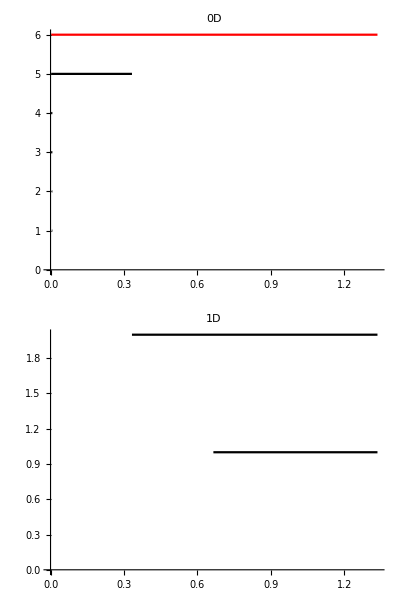

```mathematica
Column[ReadBarcodeDiagrams["example2D"],Frame->All]
```

And here’s an annotated version—the short-lived connected components are pretty numerous, though.

```mathematica
Column[ReadBarcodeDiagrams["example2D",True],Frame->All]
```

-Graphics-

### Voxel data

We’ll do a few examples here in rapid-fire.

#### Off-center point source:

```mathematica
RunPerseus["ex3D_point"][Gaussian[0.5,{0.3,0.2,0.1}],0.05,{50,50,50}]
```

/Users/thomas/perseus/ex3D_point/output_*

-Graphics3D-

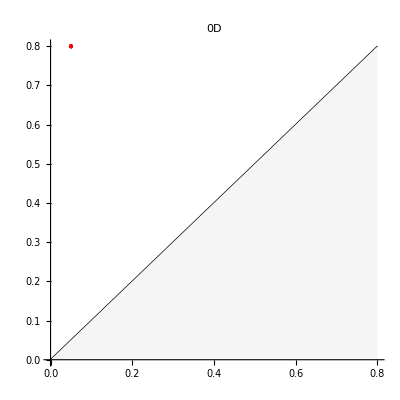
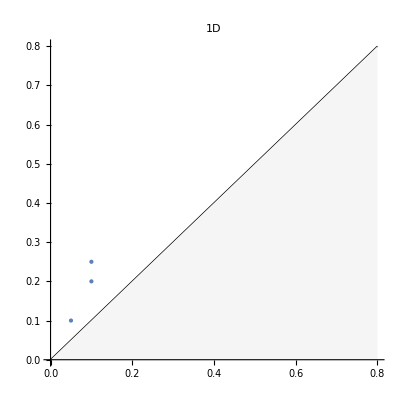
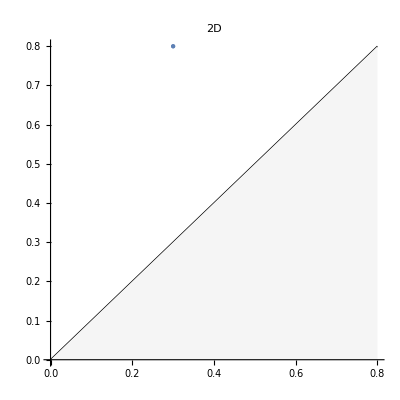

```mathematica
ReadPersistenceDiagrams["ex3D_point"]
```

Note that mousing over the callouts below will magnify them.

Here we see a notable technical phenomenon: because our very first slice was big enough, we leapfrogged over the milieu of small connected components that emerge from the corners then quickly merge (die).

In a way this is good: we don’t really care about those small generators.

Notice that all of the 1D holes have to do with holes formed on the boundary. They all die pretty quickly, and you can see above that they’re pretty close to the diagonal.

The important feature is the 2D hole formed when the point source creates a void.

```mathematica
Column[ReadBarcodeDiagrams["ex3D_point",True],Frame->All]
```

-Graphics-

#### Off-kilter double gaussian:

```mathematica
RunPerseus["ex3D_double"][{x,y,z}|->Gaussian[0.15,{0.4,0.3,0.2}][x,y,z]+Gaussian[0.2,{-0.35,0.25,0.15}][x,y,z],0.05,{50,50,50}]
```

/Users/thomas/perseus/ex3D_double/output_*

-Graphics3D-

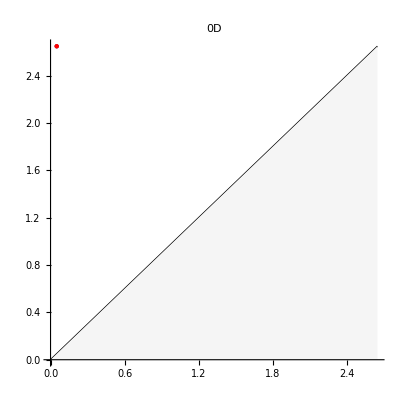
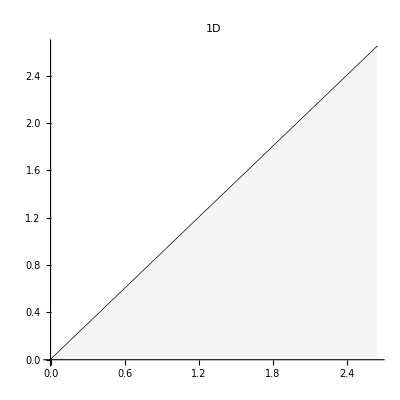
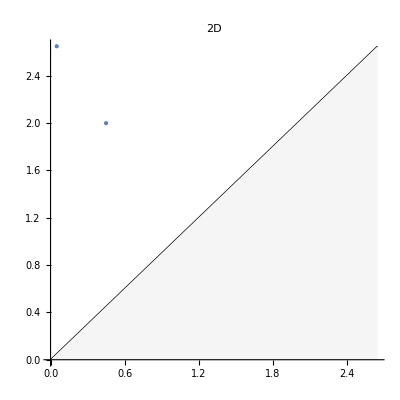

```mathematica
ReadPersistenceDiagrams["ex3D_double"]
```

Similarly to the previous example, the Gaussian is small enough at the boundary that our first slice leapfrogs over the 0D swarm—but here it also jumps over the 1D boundary effects as well.

We can see that there are two 2D holes: one is formed immediately and lives a long time, the “compound bubble”; and one is formed at the next critical point, when the bubble pinches in two.

Note also that the compound bubble is considered to have lasted longer (died later than) the smaller bubble. This is an “arbitrary choice” in some sense, but is deterministic and by design, since we’re looking for the features that last the longest.

This also means that we can answer the question “which holes, exactly, are the two (2D) holes?”: the long-lived one is the hole that encloses both voids, and the shorter-lived one is the hole that closes up first.

If you mouse over the plot for the death time of the shorter-lived 2D generator, you’ll see a tiny bubble still present...it’s the other one that died at this point.

```mathematica
Column[ReadBarcodeDiagrams["ex3D_double",True],Frame->All]
```

-Graphics-

#### Centered shell

This is nonzero at the center, then rises radially, then drops to zero at infinity.

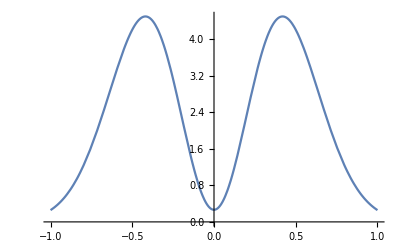

```mathematica
Plot[Gaussian[0.3,{0}][x](0.2+50*x^2),{x,-1,1}]
```

If you change c to make it off-center, you’ll see some more boundary noise appear.

```mathematica
With[{c={0,0,0}},RunPerseus["ex3D_shell"][{x,y,z}|->Gaussian[0.3,c][x,y,z](0.2+50*Norm[{x,y,z}-c]^2),0.05,{50,50,50}]]
```

/Users/thomas/perseus/ex3D_shell/output_*

-Graphics3D-

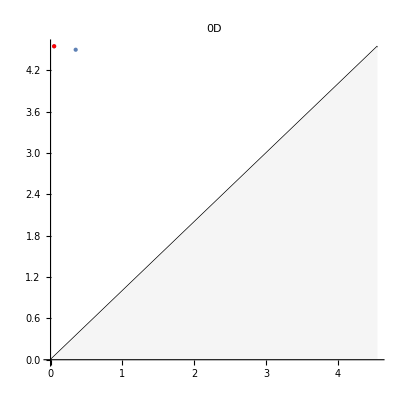
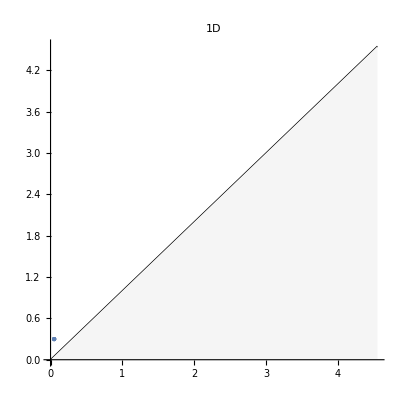
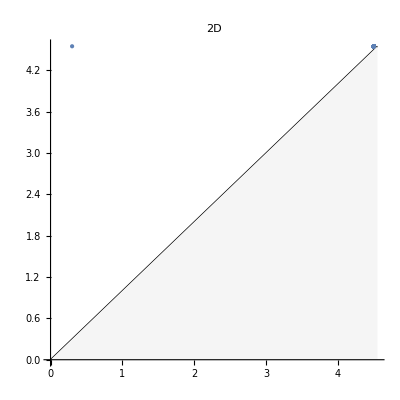

```mathematica
ReadPersistenceDiagrams["ex3D_shell"]
```

The notable thing here is the two long-lived connected components: one for the outside the shell, one for the inside.

The short-lived 1D generators and the short-lived 1D/2D generators near the end are boundary noise and discretization noise.

But note how many noisy (2D) generators there are! That point in the upper right is really many points superimposed.

```mathematica
ReadPersistenceOutput["ex3D_shell"]
```

{{{7,90},{1,-1}},{{1,6},{1,6},{1,6},{1,6},{1,6}},{{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{90,91},{6,91}},{}}

What’s going on here?

It's a discretization issue—the cells shown below are the last to be filled in. You can see how if each of these was a void, it would mean loads of little 2D holes.

```mathematica
With[{f={x,y,z}|->Gaussian[0.3,{0,0,0}][x,y,z](0.2+50*Norm[{x,y,z}]^2)},ListDensityPlot3D[PreprocessValues[Array[f,{50,50,50},{{-1,1},{-1,1},{-1,1}}],0.05],RegionFunction->(#4==91&)]]
```

-Graphics3D-

We’re going to clean up by eliminating pairs with a lifetime less than 10% of the max (for good measure).

Note: If I recall correctly, there is a formal sense in which having a lifetime cutoff is the “right” way to handle noise.

This also gets rid of those boundary-noise 1D generators.

```mathematica
Column[ReadBarcodeDiagrams["ex3D_shell",True,DeleteCases[#1,{x_Integer,y_Integer?Positive}/;y-x<=0.1*#3["imMax"]]&],Frame->All]
```

-Graphics-

### Okay! And what else?

That’s a quick intro to persistent homology using Perseus!

Perseus can also handle more abstract shapes beyond n-dimensional cubical data, such as triangulated manifolds, abstract complexes, etc.

Perseus seems to build the discrete Morse complex associated with the full shape in the course of calculating the persistent homology—or perhaps it does some kind of reduction.

Either way, it throws this information away...but I wish it wouldn’t.

That discrete Morse complex contains much of the same information as the persistent homology, but includes some important relationships which we’ve lost here.

For example, in our very first example, with two Gaussians, we couldn’t distinguish between critical points on the boundary and the saddle point in the middle—both just created a 1D hole (and one merged two connected components). But the Morse complex, in principle, retains this information.

I also think that the basic handling of persistent homology doesn’t talk about boundary phenomena very well. Phenomena that occur because we’re sampling a finite rectangle of infinite space should be separated from phenomena “in the bulk”.

Further, you might have noticed that we made a very arbitrary choice here: we asked for all pixels less than a specific threshold value, and filled in the image by increasing the threshold value—but could just as well have asked for all pixels greater than a specific threshold value, and filled in the image by decreasing the threshold value!

In general, it’s difficult to connect the results of these two approaches.

I haven’t dug very far into this, but I think “zig-zag” homology (a real thing) might be a (the?) way of unifying the two approaches.

And finally, a small technical note:

In Perseus, we implicitly realize pixels as squares, voxels as cubes, etc. This means that two diagonally-adjacent pixels are considered to be "connected" (by their overlapping vertex).

We could have instead represented pixels as points, with edges between adjacent pixels, and squares filling in the space between four pixels. Here, a square only enters when all four of its pixels enter. So, two diagonally-separated pixels are not considered touching.

It turns out you can interpolate between these two approaches geometrically, and this induces a (sometimes nontrivial) interpolation between the persistence diagrams.

(This was the focus of my research, but I never published it. Maybe I should, somehow...)

Anyway, statistics can be done to identify phenomena from their persistence diagrams, for example.

I’m personally a little out of the loop now, so it’s possible my concerns are all addressed somewhere, somehow.

But in the meantime, it’s still pretty neat that you can extract topological features from data in such a concrete form! :)